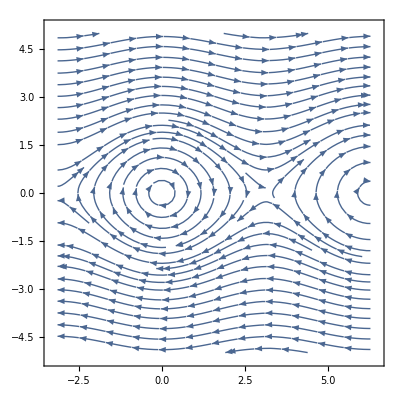
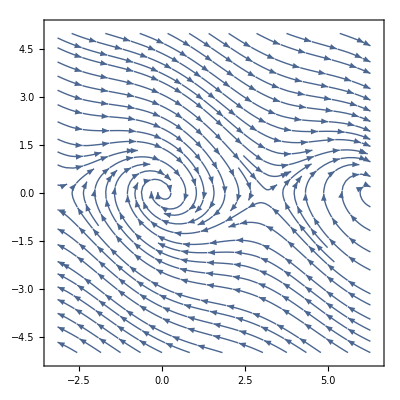
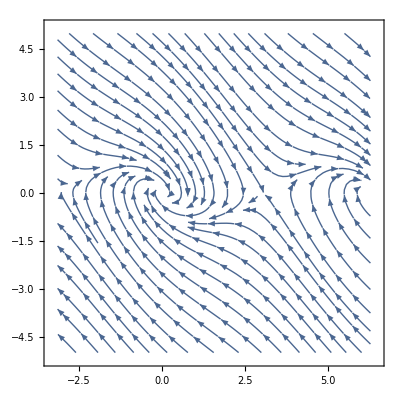
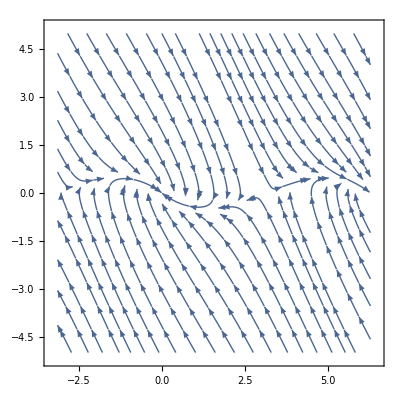
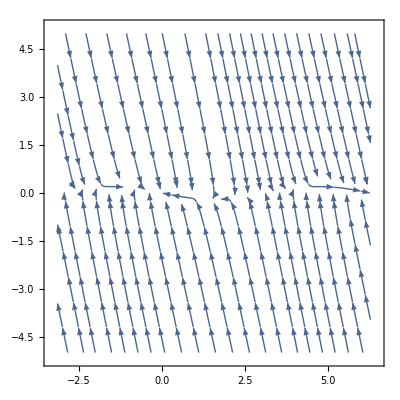
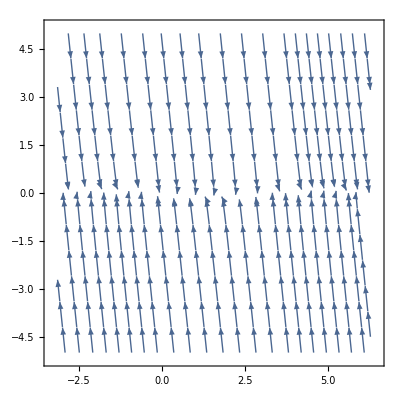

```mathematica
xDot=.
yDot=.
xDot[x_,y_,σ_]:=y
yDot[x_,y_,σ_]:=-Sin[x]-σ y
Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-π,2*π}, {y,-5,5}],{σ,{0,0.5,1,2,5,10}}]
```

```mathematica
Solve[{xDot[x,y,σ] == 0, yDot[x,y,σ]==0}]
```

{{y→0,x→ConditionalExpression[2 π C[1],C[1]∈ℤ]},{y→0,x→ConditionalExpression[π+2 π C[1],C[1]∈ℤ]}}

```mathematica
J[x_,y_]={{D[xDot[x,y,σ],x], D[xDot[x,y,σ],y]},{D[yDot[x,y,σ],x],D[yDot[x,y,σ],y]}}
taus[x_,y_] = Tr[J[x,y]]
deltas[x_,y_] = Det[J[x,y]]
lambdas[x_,y_]=Eigenvalues[J[x,y]]
eigenvectors[x_,y_]=Eigenvectors[J[x,y]]
```

{{0,1},{-Cos[x],-σ}}

-σ

Cos[x]

{1/2 (-σ-√(σ^2-4 Cos[x])),1/2 (-σ+√(σ^2-4 Cos[x]))}

{{1/2 (-σ Sec[x]+Sec[x] √(Cos[x] (-4+σ^2 Sec[x]))),1},{1/2 (-σ Sec[x]-Sec[x] √(Cos[x] (-4+σ^2 Sec[x]))),1}}

```mathematica
tg = TextGrid[{{"Fixed point (x*,y*)","(0,0)", "(π,0)"},{"τ",taus[0,0],taus[π,0]},{"Δ",deltas[0,0], deltas[π,0]}, {"λ",Evaluate[lambdas[0,0]], lambdas[π,0]},{"Type (σ=0)","Stable center","Saddle node"},{"Type (0<σ<2)","Stable spiral","Saddle node"},{"Type (σ=2)","Stable star","Saddle node"},{"Type (σ>2)","Stable node","Saddle node"}},Frame->All]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/table.png",tg]
```

Fixed point (x*,y*) | (0,0) | (π,0)
τ | -σ | -σ
Δ | 1 | -1
λ | {1/2 (-σ-√(-4+σ^2)),1/2 (-σ+√(-4+σ^2))} | {1/2 (-σ-√(4+σ^2)),1/2 (-σ+√(4+σ^2))}
Type (σ=0) | Stable center | Saddle node
Type (0<σ<2) | Stable spiral | Saddle node
Type (σ=2) | Stable star | Saddle node
Type (σ>2) | Stable node | Saddle node

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/table.png

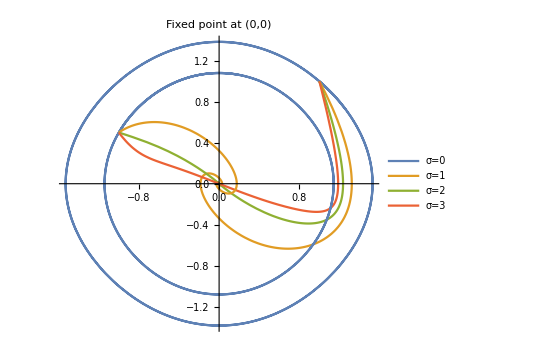

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/pend_0_0.png

```mathematica
(*sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,15}],{x0,{-1,0.5}},{y0,{-0.75,1.5}},{σ,{0,1,2,3}}];
funcs={x[t],y[t]}/.Flatten[sols,{2,3,4}];
*)
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==1,y[0]==1},{x[t],y[t]},{t,0,15}],{σ,{0,1,2,3}}];
funcs={x[t],y[t]}/.sols;
p1=ParametricPlot[funcs,{t,0,15},PlotRange->All,PlotLegends->{"σ=0","σ=1","σ=2","σ=3"}, PlotLabel->"Fixed point at (0,0)"];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==-1,y[0]==0.5},{x[t],y[t]},{t,0,15}],{σ,{0,1,2,3}}];
funcs={x[t],y[t]}/.sols;
p2=ParametricPlot[funcs,{t,0,15},PlotRange->All];
g = Show[{p1,p2}]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/pend_0_0.png",g,ImageSize->1500]
```

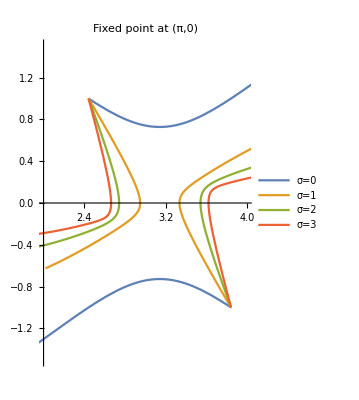

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/pend_pi_0.png

```mathematica
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π-0.7,y[0]==1},{x[t],y[t]},{t,0,5}],{σ,{0,1,2,3}}];
funcs={x[t],y[t]}/.sols;
p1=ParametricPlot[funcs,{t,0,5}, PlotRange->{{2,4},{-1.5,1.5}},PlotLegends->{"σ=0","σ=1","σ=2","σ=3"},PlotLabel->"Fixed point at (π,0)"];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π+0.7,y[0]==-1},{x[t],y[t]},{t,0,5}],{σ,{0,1,2,3}}];
funcs={x[t],y[t]}/.sols;
p2=ParametricPlot[funcs,{t,0,5}, PlotRange->{{2,4},{-1.5,1.5}}];
g = Show[{p1,p2}]
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 2/pend_pi_0.png",g,ImageSize->1500]
```